```mathematica
(*  F[1, {0}] = electron neutrino, F[1, {1}] = muon neutrino, F[1, {2}] = tau neutrino, 
	F[2, {0}] = electron, F[2, {1}] = muon, F[2, {2}] = tau,  
	F[3, {0}] = up, F[3, {1}] = charm, F[3, {2}] = top,  
	F[4, {0}] = down, F[4, {1}] = strange, F[4, {2}] = bottom, 
	V[1] = photon, V[2] = Z, V[3] = W-, S[1] = H *)
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;

MakeBoxes[p1,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(1\)]\)";
MakeBoxes[p2,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(2\)]\)";
topology = CreateTopologies[0,1->2];
```

FeynCalc 10.0.0 (dev version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

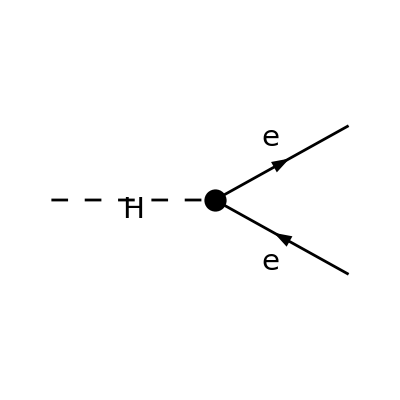

ⅈ (φ(OverBar[p_1],m_e)).(-(ⅈ e m_e)/(2 m_W (sin(θ_W)))).(φ(-OverBar[p_2],m_e))

-(e^2 (4 m_e^4-m_e^2 m_H^2))/(2 m_W^2 (sin(θ_W))^2)

v

```mathematica
(* SM: H -> lept lept *)
feynman=InsertFields[topology, {S[1]}->{F[2,{1}],-F[2,{1}]}, InsertionLevel->{Classes}];
Paint[feynman, Numbering->None,SheetHeader->False, ColumnsXRows->{4,1}, ImageSize->{1032,256}];
amplitude[0]=FCFAConvert[CreateFeynAmp[feynman],IncomingMomenta->{p},OutgoingMomenta->{p1,p2},UndoChiralSplittings->True ,ChangeDimension->4,DropSumOver->True, List->False,SMP->True,Contract->True]
FCClearScalarProducts[];
SP[p,p]=SMP["m_H"]^2;
SP[p1,p1]=SMP["m_e"]^2;
SP[p2,p2]=SMP["m_e"]^2;
SP[p1,p2]=(SMP["m_H"]^2-2 SMP["m_e"]^2)/2;
squareamplitude[0]=(amplitude[0] (ComplexConjugate[amplitude[0]]))//FeynAmpDenominatorExplicit//FermionSpinSum[#] &//DiracSimplify//Simplify
v
(* output = feynman diagrams, amplitude, squared amplitude, massless squared amplitude *)
```

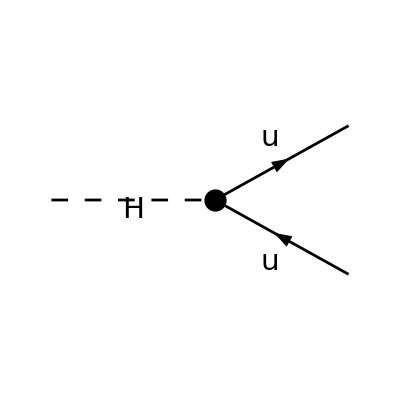

ⅈ (φ(OverBar[p_1],m_u)).(-(ⅈ e m_u δ_Col2Col3)/(2 m_W (sin(θ_W)))).(φ(-OverBar[p_2],m_u))

(e^2 C_A m_u^2 (m_H^2-4 m_u^2))/(2 m_W^2 (sin(θ_W))^2)

-(e^2 (4 m_e^4-m_e^2 m_H^2))/(2 m_W^2 (sin(θ_W))^2)

```mathematica
(* SM: H -> quark quark *)
feynman=InsertFields[topology, {S[1]}->{F[3,{1}],-F[3,{1}]}, InsertionLevel->{Classes}];
Paint[feynman, Numbering->None,SheetHeader->False, ColumnsXRows->{4,1}, ImageSize->{1032,256}];
amplitude[0]=FCFAConvert[CreateFeynAmp[feynman],IncomingMomenta->{p},OutgoingMomenta->{p1,p2},UndoChiralSplittings->True ,ChangeDimension->4,DropSumOver->True, List->False,SMP->True,Contract->True]
FCClearScalarProducts[];
SP[p,p]=SMP["m_H"]^2;
SP[p1,p1]=SMP["m_u"]^2;
SP[p2,p2]=SMP["m_u"]^2;
SP[p1,p2]=(SMP["m_H"]^2-2 SMP["m_u"]^2)/2;
squareamplitude2[0]=(amplitude[0] (ComplexConjugate[amplitude[0]]))//FeynAmpDenominatorExplicit//FermionSpinSum[#] &//DiracSimplify//Simplify //SUNSimplify
masslesssquareamplitude[0] = squareamplitude[0]//ReplaceAll[#,{SMP["m_u"]->0}]&//Simplify 
(* output = feynman diagrams, amplitude, squared amplitude, massless squared amplitude *)
```

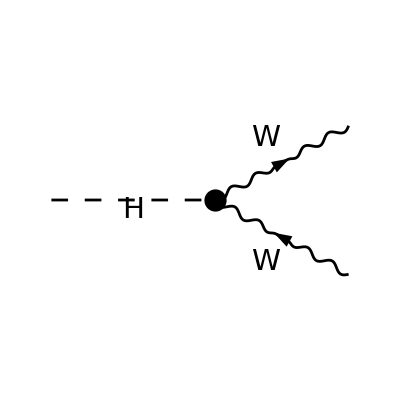

(e m_W ((ε̄)^*(p_1)·(ε̄)^*(p_2)))/(sin(θ_W))

DoPolarizationSums::failmsg: Error! DoPolarizationSums has encountered a fatal problem and must abort the computation. The problem reads: Polarization vectors do not seem to appear in a proper way in the expression.

$Aborted

```mathematica
(* SM: H -> W- W+ *)
feynman=InsertFields[topology, {S[1]}->{V[3], -V[3]}, InsertionLevel->{Classes}];
Paint[feynman, Numbering->None,SheetHeader->False, ColumnsXRows->{4,1}, ImageSize->{1032,256}];
amplitude[0]=FCFAConvert[CreateFeynAmp[feynman],IncomingMomenta->{p},OutgoingMomenta->{p1,p2},UndoChiralSplittings->True ,ChangeDimension->4,DropSumOver->True, List->False,SMP->True,Contract->True]
FCClearScalarProducts[];
SP[p,p]=SMP["m_H"]^2;
SP[p1,p1]=SMP["m_W"]^2;
SP[p2,p2]=SMP["m_W"]^2;
SP[p1,p2]=(SMP["m_H"]^2-2 SMP["m_W"]^2)/2;
squareamplitude[0]=(amplitude3[0] (ComplexConjugate[amplitude[0]]))//FeynAmpDenominatorExplicit//DoPolarizationSums[#,p1]&//DoPolarizationSums[#,p2] &//Simplify
(* output = feynman diagrams, amplitude, squared amplitude *)
```

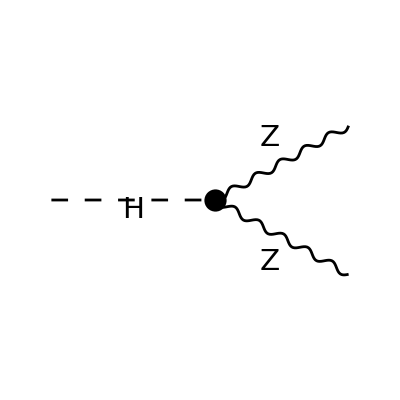

(e m_W ((ε̄)^*(p_1)·(ε̄)^*(p_2)))/((cos(θ_W))^2 (sin(θ_W)))

(e^2 m_W^2 (-4 m_H^2 m_Z^2+m_H^4+12 m_Z^4))/(4 m_Z^4 (cos(θ_W))^4 (sin(θ_W))^2)

```mathematica
(* SM: H -> Z Z *)
feynman=InsertFields[topology, {S[1]}->{V[2], V[2]}, InsertionLevel->{Classes}];
Paint[feynman, Numbering->None,SheetHeader->False, ColumnsXRows->{4,1}, ImageSize->{1032,256}];
amplitude[0]=FCFAConvert[CreateFeynAmp[feynman],IncomingMomenta->{p},OutgoingMomenta->{p1,p2},UndoChiralSplittings->True ,ChangeDimension->4,DropSumOver->True, List->False,SMP->True,Contract->True]
FCClearScalarProducts[];
SP[p,p]=SMP["m_H"]^2;
SP[p1,p1]=SMP["m_Z"]^2;
SP[p2,p2]=SMP["m_Z"]^2;
SP[p1,p2]=(SMP["m_H"]^2-2 SMP["m_Z"]^2)/2;
squareamplitude[0]=(amplitude[0] (ComplexConjugate[amplitude[0]]))//FeynAmpDenominatorExplicit//DoPolarizationSums[#,p1]&//DoPolarizationSums[#,p2] &//Simplify
(* output = feynman diagrams, amplitude, squared amplitude *)
```

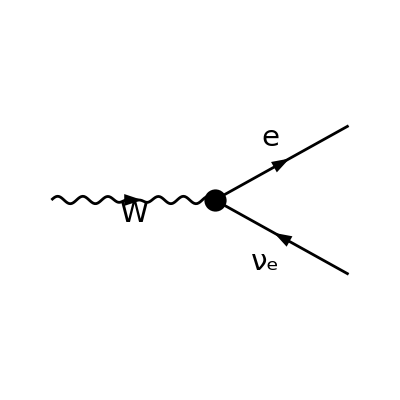

-(e (φ(OverBar[p_1],m_e)).(γ̄·ε̄(p)).(γ̄)^7.(φ(-OverBar[p_2])))/(√2 (sin(θ_W)))

-(e^2 (m_e^2 m_W^2+m_e^4-2 m_W^4))/(6 m_W^2 (sin(θ_W))^2)

(e^2 m_W^2)/(3 (sin(θ_W))^2)

```mathematica
(* SM: W- -> e- nu *)
feynman=InsertFields[topology, {V[3]}->{F[2,{1}],-F[1,{1}]}, InsertionLevel->{Classes}];
Paint[feynman, Numbering->None,SheetHeader->False, ColumnsXRows->{4,1}, ImageSize->{1032,256}];
amplitude[0]=FCFAConvert[CreateFeynAmp[feynman],IncomingMomenta->{p},OutgoingMomenta->{p1,p2},UndoChiralSplittings->True ,ChangeDimension->4,DropSumOver->True, List->False,SMP->True,Contract->True]
FCClearScalarProducts[];
SP[p,p]=SMP["m_W"]^2;
SP[p1,p1]=SMP["m_e"]^2;
SP[p2,p2]=0;
SP[p1,p2]=(SMP["m_W"]^2-SMP["m_e"]^2)/2;
SP[p,p1]=SP[p1,p1] + SP[p2,p1];
SP[p,p2]=SP[p1,p2] + SP[p2,p2];
squareamplitude[0]=(amplitude[0] (ComplexConjugate[amplitude[0]]))//FeynAmpDenominatorExplicit//FermionSpinSum[#] &//DiracSimplify//DoPolarizationSums[#,p, ExtraFactor->1/3]&//Simplify
masslesssquareamplitude[0] = squareamplitude[0]//ReplaceAll[#,{SMP["m_e"]->0}]&//Simplify 
(* output = feynman diagrams, amplitude, squared amplitude, massless squared amplitude *)
```

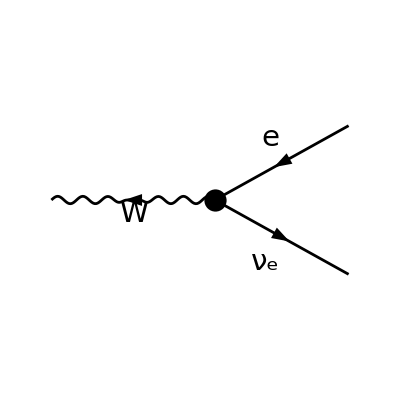

(e (φ(OverBar[p_2])).(γ̄·ε̄(p)).(γ̄)^7.(φ(-OverBar[p_1],m_e)))/(√2 (sin(θ_W)))

-(e^2 (m_e^2 m_W^2+m_e^4-2 m_W^4))/(6 m_W^2 (sin(θ_W))^2)

(e^2 m_W^2)/(3 (sin(θ_W))^2)

```mathematica
(* SM: W+ -> e+ nu *)
feynman=InsertFields[topology, {-V[3]}->{-F[2,{1}],F[1,{1}]}, InsertionLevel->{Classes}];
Paint[feynman, Numbering->None,SheetHeader->False, ColumnsXRows->{4,1}, ImageSize->{1032,256}];
amplitude[0]=FCFAConvert[CreateFeynAmp[feynman],IncomingMomenta->{p},OutgoingMomenta->{p1,p2},UndoChiralSplittings->True ,ChangeDimension->4,DropSumOver->True, List->False,SMP->True,Contract->True]
FCClearScalarProducts[];
SP[p,p]=SMP["m_W"]^2;
SP[p1,p1]=SMP["m_e"]^2;
SP[p2,p2]=0;
SP[p1,p2]=(SMP["m_W"]^2-SMP["m_e"]^2)/2;
SP[p,p1]=SP[p1,p1] + SP[p2,p1];
SP[p,p2]=SP[p1,p2] + SP[p2,p2];
squareamplitude[0]=(amplitude[0] (ComplexConjugate[amplitude[0]]))//FeynAmpDenominatorExplicit//FermionSpinSum[#] &//DiracSimplify//DoPolarizationSums[#,p, ExtraFactor->1/3]&//Simplify
masslesssquareamplitude[0] = squareamplitude[0]//ReplaceAll[#,{SMP["m_e"]->0}]&//Simplify 
(* output = feynman diagrams, amplitude, squared amplitude, massless squared amplitude *)
```

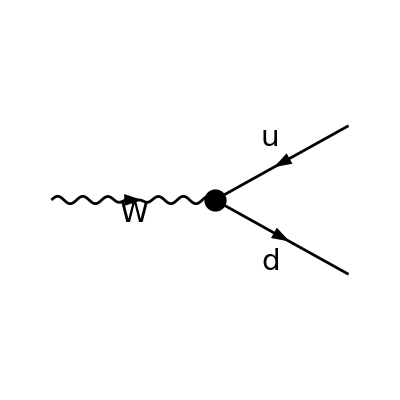

(e δ_Col2Col3 (φ(OverBar[p_2],m_d)).(γ̄·ε̄(p)).(γ̄)^7.(φ(-OverBar[p_1],m_u)))/(√2 (sin(θ_W)))

-(e^2 C_A (m_d^2 (m_W^2-2 m_u^2)+m_d^4+m_u^2 m_W^2+m_u^4-2 m_W^4))/(6 m_W^2 (sin(θ_W))^2)

(e^2 C_A m_W^2)/(3 (sin(θ_W))^2)

```mathematica
(* SM: W- -> d antiu *)
feynman=InsertFields[topology, {V[3]}->{-F[3,{1}],F[4,{1}]}, InsertionLevel->{Classes}];
Paint[feynman, Numbering->None,SheetHeader->False, ColumnsXRows->{4,1}, ImageSize->{1032,256}];
amplitude[0]=FCFAConvert[CreateFeynAmp[feynman],IncomingMomenta->{p},OutgoingMomenta->{p1,p2},UndoChiralSplittings->True ,ChangeDimension->4,DropSumOver->True, List->False,SMP->True,Contract->True]
FCClearScalarProducts[];
SP[p,p]=SMP["m_W"]^2;
SP[p1,p1]=SMP["m_u"]^2;
SP[p2,p2]=SMP["m_d"]^2;
SP[p1,p2]=(SMP["m_W"]^2-SMP["m_u"]^2 -SMP["m_d"]^2)/2;
SP[p,p1]=SP[p1,p1] + SP[p2,p1];
SP[p,p2]=SP[p1,p2] + SP[p2,p2];
squareamplitude[0]=(amplitude[0] (ComplexConjugate[amplitude[0]]))//SUNSimplify//FermionSpinSum//DiracSimplify//DoPolarizationSums[#,p,ExtraFactor->1/3]&//Simplify
masslesssquareamplitude[0] = squareamplitude[0]//ReplaceAll[#,{SMP["m_u"]->0, SMP["m_d"]->0}]&//Simplify 
(* output = feynman diagrams, amplitude, squared amplitude, massless squared amplitude *)
```

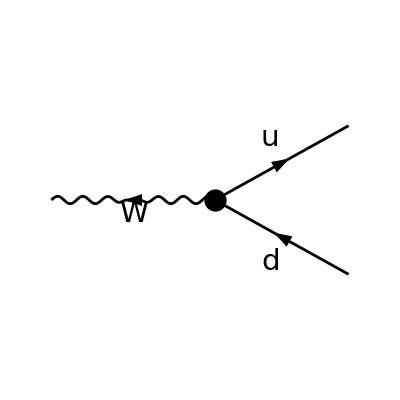

-(e δ_Col2Col3 (φ(OverBar[p_1],m_u)).(γ̄·ε̄(p)).(γ̄)^7.(φ(-OverBar[p_2],m_d)))/(√2 (sin(θ_W)))

-(e^2 C_A (m_d^2 (m_W^2-2 m_u^2)+m_d^4+m_u^2 m_W^2+m_u^4-2 m_W^4))/(6 m_W^2 (sin(θ_W))^2)

(e^2 C_A m_W^2)/(3 (sin(θ_W))^2)

```mathematica
(* SM: W+ -> u antid *)
feynman=InsertFields[topology, {-V[3]}->{F[3,{1}],-F[4,{1}]}, InsertionLevel->{Classes}];
Paint[feynman, Numbering->None,SheetHeader->False, ColumnsXRows->{4,1}, ImageSize->{1032,256}];
amplitude[0]=FCFAConvert[CreateFeynAmp[feynman],IncomingMomenta->{p},OutgoingMomenta->{p1,p2},UndoChiralSplittings->True ,ChangeDimension->4,DropSumOver->True, List->False,SMP->True,Contract->True]
FCClearScalarProducts[];
SP[p,p]=SMP["m_W"]^2;
SP[p1,p1]=SMP["m_u"]^2;
SP[p2,p2]=SMP["m_d"]^2;
SP[p1,p2]=(SMP["m_W"]^2-SMP["m_u"]^2 -SMP["m_d"]^2)/2;
SP[p,p1]=SP[p1,p1] + SP[p2,p1];
SP[p,p2]=SP[p1,p2] + SP[p2,p2];
squareamplitude[0]=(amplitude[0] (ComplexConjugate[amplitude[0]]))//SUNSimplify//FermionSpinSum//DiracSimplify//DoPolarizationSums[#,p,ExtraFactor->1/3]&//Simplify
masslesssquareamplitude[0] = squareamplitude[0]//ReplaceAll[#,{SMP["m_u"]->0, SMP["m_d"]->0}]&//Simplify 
(* output = feynman diagrams, amplitude, squared amplitude, massless squared amplitude *)
```

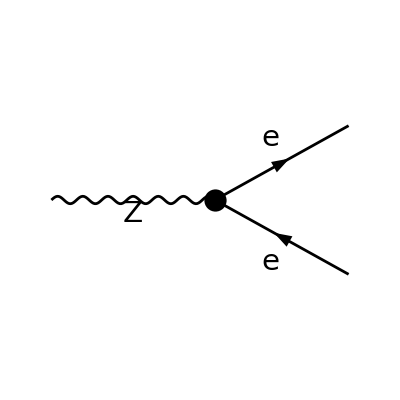

ⅈ (φ(OverBar[p_1],m_e)).((ⅈ e (sin(θ_W)) (γ̄·ε̄(p)).(γ̄)^6)/(cos(θ_W))+(ⅈ e ((sin(θ_W))^2-1/2) (γ̄·ε̄(p)).(γ̄)^7)/((cos(θ_W)) (sin(θ_W)))).(φ(-OverBar[p_2],m_e))

(e^2 (m_e^2 (16 (sin(θ_W))^4-8 (sin(θ_W))^2-1)+m_Z^2 (8 (sin(θ_W))^4-4 (sin(θ_W))^2+1)))/(6 (cos(θ_W))^2 (sin(θ_W))^2)

(e^2 m_Z^2 (8 (sin(θ_W))^4-4 (sin(θ_W))^2+1))/(6 (cos(θ_W))^2 (sin(θ_W))^2)

```mathematica
(* SM: Z -> e- e+ *)
feynman=InsertFields[topology, {V[2]}->{F[2,{1}],-F[2,{1}]}, InsertionLevel->{Classes}];
Paint[feynman, Numbering->None,SheetHeader->False, ColumnsXRows->{4,1}, ImageSize->{1032,256}];
amplitude[0]=FCFAConvert[CreateFeynAmp[feynman],IncomingMomenta->{p},OutgoingMomenta->{p1,p2},UndoChiralSplittings->True ,ChangeDimension->4,DropSumOver->True, List->False,SMP->True,Contract->True]
FCClearScalarProducts[];
SP[p,p]=SMP["m_Z"]^2;
SP[p1,p1]=SMP["m_e"]^2;
SP[p2,p2]=SMP["m_e"]^2;
SP[p1,p2]=(SMP["m_Z"]^2-2 SMP["m_e"]^2)/2;
SP[p,p1]=SP[p1,p1] + SP[p2,p1];
SP[p,p2]=SP[p1,p2] + SP[p2,p2];
squareamplitude[0]=(amplitude[0] (ComplexConjugate[amplitude[0]]))//FeynAmpDenominatorExplicit//FermionSpinSum[#] &//DiracSimplify//DoPolarizationSums[#,p, ExtraFactor->1/3]&//Simplify
masslesssquareamplitude[0] = squareamplitude[0]//ReplaceAll[#,{SMP["m_e"]->0}]&//Simplify 
(* output = feynman diagrams, amplitude, squared amplitude, massless squared amplitude *)
```

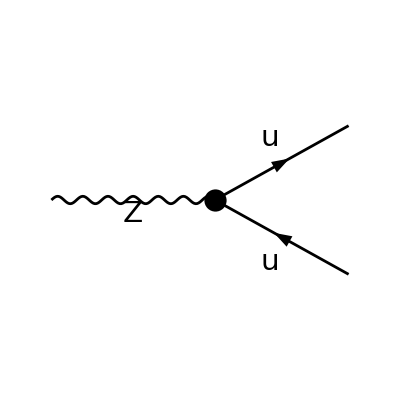

ⅈ (φ(OverBar[p_1],m_u)).((ⅈ e δ_Col2Col3 (1/2-2/3 (sin(θ_W))^2) (γ̄·ε̄(p)).(γ̄)^7)/((cos(θ_W)) (sin(θ_W)))-(2 ⅈ e δ_Col2Col3 (sin(θ_W)) (γ̄·ε̄(p)).(γ̄)^6)/(3 (cos(θ_W)))).(φ(-OverBar[p_2],m_u))

(e^2 C_A (m_u^2 (64 (sin(θ_W))^4-48 (sin(θ_W))^2-9)+m_Z^2 (32 (sin(θ_W))^4-24 (sin(θ_W))^2+9)))/(54 (cos(θ_W))^2 (sin(θ_W))^2)

(e^2 C_A m_Z^2 (32 (sin(θ_W))^4-24 (sin(θ_W))^2+9))/(54 (cos(θ_W))^2 (sin(θ_W))^2)

```mathematica
(* SM: Z -> u antiu *)
feynman=InsertFields[topology, {V[2]}->{F[3,{1}],-F[3,{1}]}, InsertionLevel->{Classes}];
Paint[feynman, Numbering->None,SheetHeader->False, ColumnsXRows->{4,1}, ImageSize->{1032,256}];
amplitude[0]=FCFAConvert[CreateFeynAmp[feynman],IncomingMomenta->{p},OutgoingMomenta->{p1,p2},UndoChiralSplittings->True ,ChangeDimension->4,DropSumOver->True, List->False,SMP->True,Contract->True]
FCClearScalarProducts[];
SP[p,p]=SMP["m_Z"]^2;
SP[p1,p1]=SMP["m_u"]^2;
SP[p2,p2]=SMP["m_u"]^2;
SP[p1,p2]=(SMP["m_Z"]^2-2 SMP["m_u"]^2)/2;
SP[p,p1]=SP[p1,p1] + SP[p2,p1];
SP[p,p2]=SP[p1,p2] + SP[p2,p2];
squareamplitude[0]=(amplitude[0] (ComplexConjugate[amplitude[0]]))//SUNSimplify//FermionSpinSum//DiracSimplify//DoPolarizationSums[#,p,ExtraFactor->1/3]&//Simplify
masslesssquareamplitude[0] = squareamplitude[0]//ReplaceAll[#,{SMP["m_u"]->0}]&//Simplify 
(* output = feynman diagrams, amplitude, squared amplitude, massless squared amplitude *)
```

```mathematica
Print["\tCPU Time used: ",Round[N[TimeUsed[],4],0.001]," s."];
```

CPU Time used: 4.122 s.

```mathematica
FeynCalcHowToCite[]
```

• V. Shtabovenko, R. Mertig and F. Orellana, arXiv:2312.14089.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

Null